# Unit 2: Differentiation

## Linear approximation

```mathematica
10*0.4+150
```

154.

```mathematica
D[√x,x]
```

1/(2 √x)

```mathematica
1/(2 √100)
```

1/20

```mathematica
4*%
```

1/5

```mathematica
f[x_]:=x^2.5
f'[4]*-0.03+f[4]
```

31.4

```mathematica
D[√x,{x,2}]
```

-1/(4 x^(3/2))

```mathematica
-1/(4 100^(3/2))
```

-1/4000

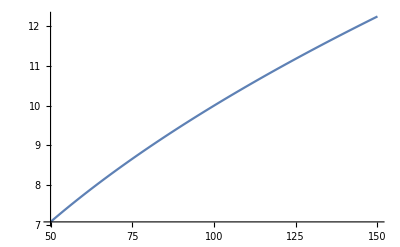

```mathematica
Plot[√x,{x,50,150}]
```

```mathematica
v[x_]:=4π*x^3/3
v'[r]
v'[10]*-0.03
```

4 π r^2

-37.6991

```mathematica
v'[10]
```

400 π

```mathematica
20/400
```

1/20

## Product rule

```mathematica
D[√x,x]*Cos[x]+√x*-Sin[x]
```

Cos[x]/(2 √x)-√x Sin[x]

```mathematica
100*0.4
```

40.

```mathematica
100*-0.01+3*0.4
```

0.2

f(x)=x^2 Sin[x]Cos[x]
f'[x]=2x*Sin[x]*Cos[x]
		 + x^2*-Cos[x] *Sin[x]
	 	+ x^2* Sin[x]*-Sin[x]

## Quotient Rule

```mathematica
Limit[(f2*g-f*g2)/t,t->0]
```

Indeterminate

```mathematica
D[(2+Cos[X])/(x^2+1),x]
```

-(2 x (2+Cos[X]))/((1+x^2)^2)